In this notebook, we study the tradeoffs between natural and adversarial accuracy.
We use the following data model.
	• Y is sampled uniformly from {True, False}.
	• X = (X_1, X_2)
	• X_1=Y
	• X_2=Y with probability p and ¬Y with probability (1 - p).

Our threat model allows the adversary to arbitrarily perturb X_1, but the adversary cannot modify X_2
We consider randomized classifiers f from X to Y below, and as notation:
			a = P(f(0, 0) = 1), b = P(f(0, 1) = 1), c = P(f(1, 0) = 1), d = P(f(1, 1) = 1).

```mathematica
natAcc[p_,a_,b_,c_,d_]:=1/2(p(1-a)+(1-p)(1-b))+1/2((1-p)c+p d)
advAcc[p_,a_,b_,c_,d_]:=(
      1/2(p Min[1-a,1-c]+(1-p)Min[1-b,1-d])
+ 1/2((1-p)Min[a,c]+p Min[b,d])
)
natAdvAccs[p_,a_,b_,c_,d_]:={natAcc[p,a,b,c,d],advAcc[p,a,b,c,d] }
natAdvAccs[p,0,0, 1, 1]
```

{1,0}

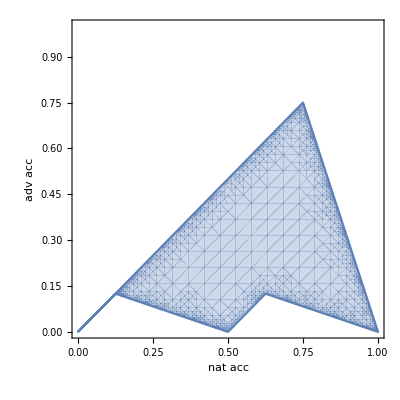

```mathematica
achievableAccs[p_]:= FunctionRange[
{
natAdvAccs[p,a,b,c,d],
0≤a≤1,0≤b≤1,0≤c≤1,0≤d≤1
},
{a,b,c,d},
{nat,adv},
Method->{"Reduced"->True}
]
accRegion=achievableAccs[3/4];
RegionPlot[
accRegion,{nat, 0, 1}, {adv, 0, 1},
PerformanceGoal->"Quality",MaxRecursion->5,
FrameLabel->{"nat acc", "adv acc"}
]
```

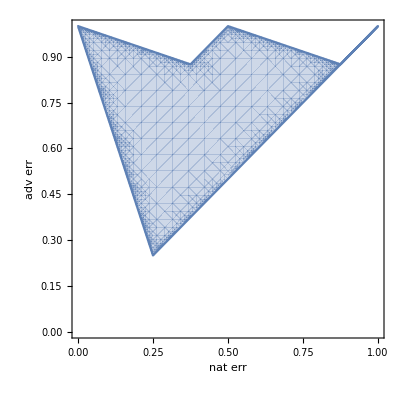

```mathematica
achievableErrs[p_]:= FunctionRange[
{
1-natAdvAccs[p,a,b,c,d],
0≤a≤1,0≤b≤1,0≤c≤1,0≤d≤1
},
{a,b,c,d},
{nat,adv},
Method->{"Reduced"->True}
]
errRegion=achievableErrs[3/4];
RegionPlot[
errRegion,{nat, 0, 1}, {adv, 0, 1},
PerformanceGoal->"Quality",MaxRecursion->5,
FrameLabel->{"nat err", "adv err"}
]
```